#### Preamble

```mathematica
ClearAll @@ {$ContextPath<>"*"}
SaveTask = CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]], 15*60];
StartScheduledTask[SaveTask]
SetDirectory[NotebookDirectory[]]
```

ScheduledTaskObject[…]

/home/juanathan/Documents/Wolfram/Wolfram_scripts/KrKr

## Kramers Kronig

```mathematica
data = Drop[Import["anexoT1.txt","Data"],1];(*[[omega, ImEps]]*)
func = Interpolation[data];
dx = 0.01;
omega = Range[0,6,dx];
imchi = func[omega];
```

### ReChi[frq_List, imchi_List, dx_Real]

#### Visualization

```mathematica
den = Table[x^2-w^2 ,{x,omega},{w,omega}];
den = ReplacePart[den, {i_, i_} -> 1];
num = Table[chi * x,{chi,imchi}, {x,omega}];
num = ReplacePart[num, {i_, i_} -> 0];
```

```mathematica
ArrayPlot[#,PlotLegends->Automatic,ImageSize->100]& /@ {den,num,1/den, num/den}
ArrayPlot[#,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->100]& /@ {den,num,1/den, num/den}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

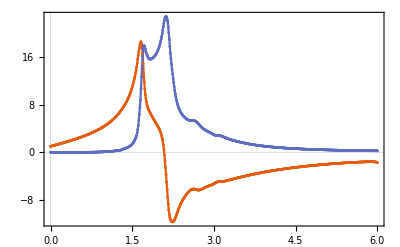

```mathematica
rechi = 1 + (2/Pi) * dx * Plus @@ (num/den);
ListPlot[{rechi,imchi},DataRange->omega[[{1,-1}]], Joined->True, Mesh->Full,PlotRange->All,PlotTheme->"Scientific"]
```

#### Function

```mathematica
ReChi[frq_List, chidata_List, dx_Real]:=Module[{den, reNum},
  
  den = ReplacePart[Table[x^2-w^2 ,{x,frq},{w,frq}], {i_, i_} -> 1]; 
  reNum = ReplacePart[Table[chi * x,{chi,chidata}, {x,frq}], {i_, i_} -> 0];
  
  1. + (2./Pi) * dx * Plus @@ (reNum/den)]
```

```mathematica
rechi = ReChi[omega, imchi ,dx];
ListPlot[{rechi,imchi},DataRange->omega[[{1,-1}]], Joined->True, Mesh->Full,PlotRange->All,PlotTheme->"Scientific"]
```

-Graphics-

### ImChi[frq_List, rechi_List, dx_Real]

#### Visualization

```mathematica
den = Table[x^2-w^2 ,{x,omega},{w,omega}];
den = ReplacePart[den, {i_, i_} -> 1];
num = Table[chi - 1,{chi,rechi}, {x,omega}];
num = ReplacePart[num, {i_, i_} -> 0];
```

```mathematica
ArrayPlot[#,PlotLegends->Automatic,ImageSize->100]& /@ {den,num,1/den, num/den}
ArrayPlot[#,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->100]& /@ {den,num,1/den, num/den}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

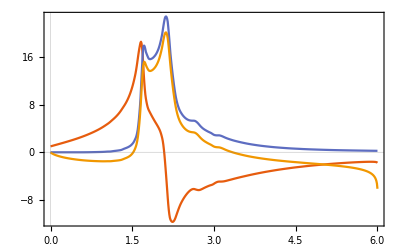

```mathematica
imchi2 = -(2/Pi) * dx * omega * Plus @@ (num/den);
ListPlot[{rechi,imchi,imchi2},DataRange->omega[[{1,-1}]], Joined->True,PlotRange->All,PlotTheme->"Scientific"]
```

#### Function

```mathematica
ImChi[frq_List, chidata_List, dx_Real]:=Module[{den, imNum},
 
  den = ReplacePart[Table[x^2-w^2 ,{x,frq},{w,frq}], {i_, i_} -> 1]; 
  imNum = ReplacePart[Table[chi - 1.,{chi,chidata}, {x,frq}], {i_, i_} -> 0];
  
  -(2./Pi) * dx * frq * Plus @@ (imNum/den)]
```

```mathematica
imchi2 = ImChi[omega,rechi,dx];
ListPlot[{rechi,imchi,imchi2},DataRange->omega[[{1,-1}]], Joined->True,PlotRange->All,PlotTheme->"Scientific"]
```

-Graphics-

### ChiRefined[frq_List, imchi_List, dx_Real]

```mathematica
ChiRefined[frq_List, rechi_List, imchi_List, dx_Real, mu_Real, n_Integer]:=Module[{den, reNum, imNum, rePart, imPart, dummyRe, dummyIm},
  den = ReplacePart[Table[x^2-w^2 ,{x,frq},{w,frq}], {i_, i_} -> 1]; 
  reNum = ReplacePart[Table[chi * x,{chi,#}, {x,frq}], {i_, i_} -> 0]& ;
  imNum = ReplacePart[Table[chi - 1.,{chi,#}, {x,frq}], {i_, i_} -> 0]& ;
  rePart =  1. + (2./Pi) * dx * Plus @@ (#/den) &;
  imPart =  -(2./Pi) * dx * frq * Plus @@ (#/den) &;
  
  dummyRe = rechi;
  dummyIm = imchi;
  Do[
    dummyRe = rePart @ reNum @ dummyIm;
    dummyRe = mu * rechi + (1-mu)*dummyRe;
    dummyIm = imPart @ imNum @ dummyRe;
    dummyIm = mu * imchi + (1-mu)*dummyIm,
  n];
   {dummyRe, dummyIm} ]
```

```mathematica
proof = ChiRefined[omega, rechi, imchi, dx, .8, 20];
```

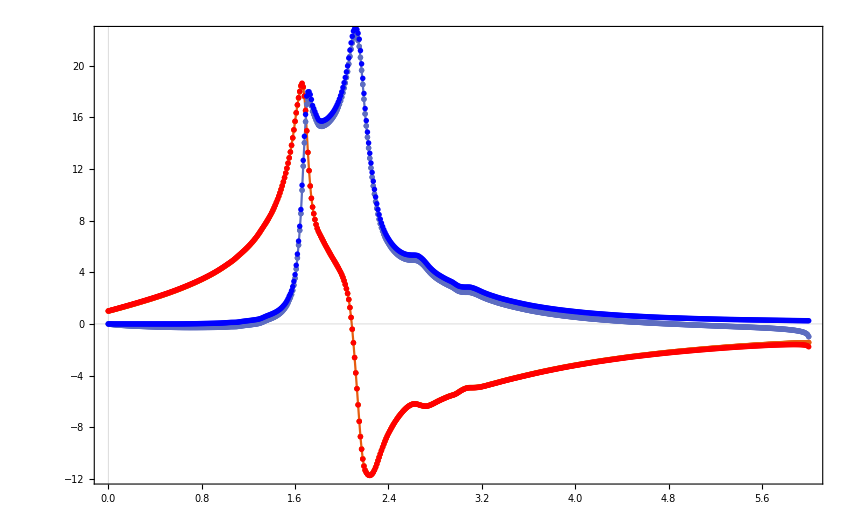

```mathematica
Show[{
ListPlot[proof,DataRange->omega[[{1,-1}]], Joined->True, Mesh->Full,PlotRange->All,PlotTheme->"Scientific"],
ListPlot[{rechi, imchi},DataRange->omega[[{1,-1}]], PlotStyle->{Red, Blue}]
}]
```

### ReChi[frq_List, imchi_List, dx_Real]

```mathematica
den = Table[x^2-w^2 ,{x,omega},{w,omega}];
den = ReplacePart[den, {i_, i_} -> 1];
num = Table[chi * x,{chi,imchi}, {x,omega}];
num = ReplacePart[num, {i_, i_} -> 0];
```

```mathematica
ReChiSubs[frq_List, chidata_List, dx_Real, {omega1_,reomega1_}]:=Module[{func, omega, den, num, imchi, rechi},
  func = Interpolation[Transpose[{frq, chidata}]];
  omega = Range @@ Flatten @ {frq[[{1,-1}]],dx};
  imchi = func[omega];
  
  den = Table[x^2-w^2 ,{x,omega},{w,omega}];
  num = Table[chi * x,{chi,imchi}, {x,omega}];
  den = ReplacePart[den, {i_, i_} -> 1];
  num = ReplacePart[num, {i_, i_} -> 0];
  
  rechi = 1 + (2/Pi) * dx * Plus @@ (num/den);
  rechi += omega
  ]
```

```mathematica
rechi = ReChi[data[[;;,1]],data[[;;,2]],dx];
ListPlot[{rechi,imchi},DataRange->omega[[{1,-1}]], Joined->True, Mesh->Full,PlotRange->All,PlotTheme->"Scientific"]
```

-Graphics-